# Problem Set 19

# EIWL Sections 43 (no problems) and 44

## 4/4 Due to getting a little behind in the final two weeks of the semester, I only checked for completeness on PS 18-21. ~Brian

## Section 43

I saw no practice problems, but I read the chapter.

## Section 44

```mathematica
Import["http://www.google.com","Images"]
```

{-Graphics-}

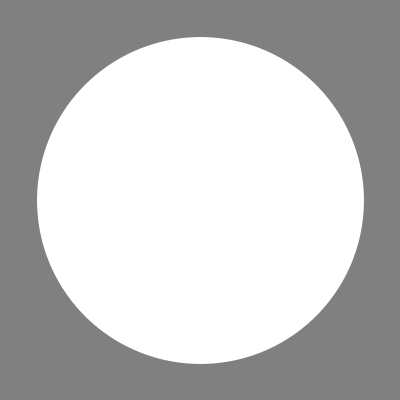
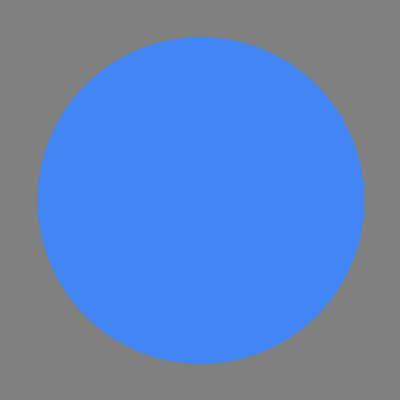
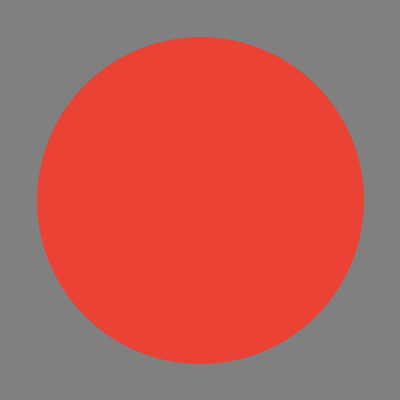
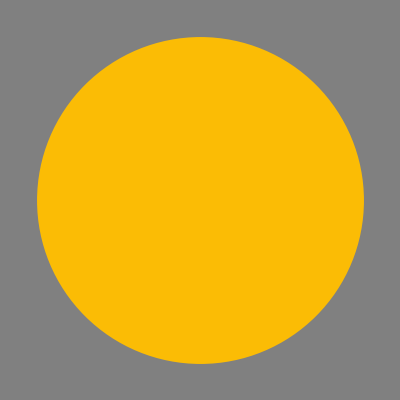
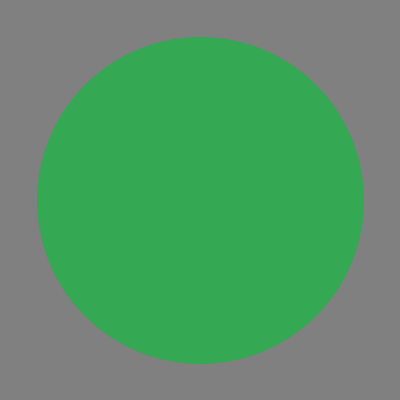

```mathematica
Graphics[Style[Disk[],#],Background->Gray]&/@(Flatten[DominantColors/@Import["https://www.google.com","Images"]])
```

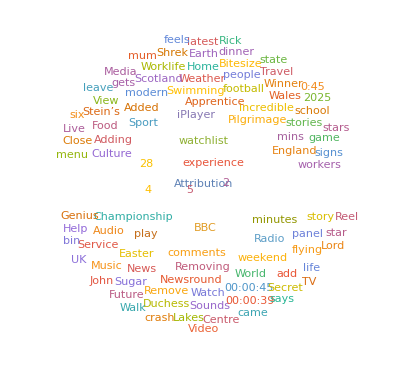

```mathematica
WordCloud[Import["https://bbc.co.uk"]]
```

```mathematica
ImageCollage[Import["https://www.nps.gov","Images"]]
```

-Graphics-

```mathematica
Select[Import["https://en.wikipedia.org/wiki/Ostrich","Images"],ImageInstanceQ[#,Entity["Species","Class:Aves"]]&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
WordCloud[TextCases[Import["https://www.nato.int/"],"Country"]]
```

-Graphics-

```mathematica
Length[Import["https://en.wikipedia.org/","Hyperlinks"]]
```

379

```mathematica
SendMail[GeoGraphics[Here]]
```

SendMail::cloudrelay: SendMail has relayed your message through the Wolfram Cloud.  A local SMTP server has not been configured. These settings can be defined through Preferences > Internet & Mail > Mail Settings in the notebook front end.

Success[…]

```mathematica
SendMail[MoonPhase[Now,"Icon"]]
```

Success[…]